Copyright (C) 2016 Leo Fang <leofang@phy.duke.edu>

This program is free software. It comes without any warranty, to the extent permitted by applicable law. You can redistribute it and/or modify it under the terms of the WTFPL, Version 2, as published by Sam Hocevar. See the accompanying LICENSE file or http://www.wtfpl.net/ for more details.

## example: plot the wavefunctions ψ and χ

In this notebook, using the sample file “k0a_0.5pi_on_new” as an example, I demonstrate how to perform post-processing of the results generated by the FDTD code.

```mathematica
(* assume the input and output files are in FDTD/examples/ *)
SetDirectory[NotebookDirectory[]<>"../examples/"]
```

```mathematica
(* read input parameters *)
Import["k0a_0.5pi_on_new"]
```

```mathematica
(* set the input parameters in the corresponding symbols *)
%//ToExpression;
```

```mathematica
(* setup based on input parameters *)
Xmin=-(Nx+nx+1)Delta;
Xmax=(Nx)Delta;
qubit1=-nx/2*Delta;
qubit2=nx/2*Delta;
```

```mathematica
(* read the absolute value of the computed two-photon wavefunction *)
χ=ReadList["k0a_0.5pi_on_new.abs_chi.out",Number,RecordLists->True];
```

```mathematica
(* plot Subscript[g, 2](τ,t)=|χ(a+Δ,a+Δ+τ,t)|^2 as an animation in time t *)
Manipulate[ListPlot[χ[[i]]^2,Joined->True,PlotMarkers->None,DataRange->{0,(Nx-nx/2+1)Delta*gamma},PlotRange->{0,All},GridLines->{{(qubit2-qubit1)*gamma},None},
PlotLabel->"t="<>ToString[(Nx+nx/2+1)+(Tstep+1)(i-1)]<>"Δ",AxesLabel->{"Γτ","g_2(τ,t)"}],{i,1,Length[χ],1}]
```

```mathematica
(* plot Subscript[g, 2](τ,t)=|χ(a+Δ,a+Δ+τ,t)|^2 at the last snapshot *)
ListPlot[χ[[-1]]^2,Joined->True,DataRange->{0,(Nx-nx/2+1)Delta*gamma},PlotRange->{0,All},GridLines->{{(qubit2-qubit1)*gamma},None},AxesLabel->{"Γτ","g_2(τ)"}]
```

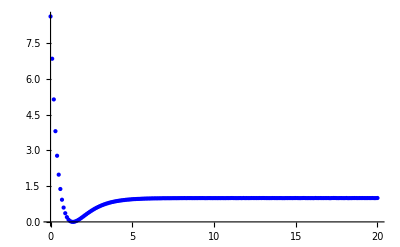
```mathematica
(* Compare with the result obtained using scattering theory; see PRA 91,053845 (2015) *)
(* note the agreement will be better when Ny≥10000 *)
Show[%,-Graphics-]
```

```mathematica
(* the next file is memory consuming, so clear some memory first *)
Clear[χ]
```

```mathematica
(* read computed wavefunctions *)
bR=ReadList["k0a_0.5pi_on_new.re.out",Number,RecordLists->True](* real part*);
bI=ReadList["k0a_0.5pi_on_new.im.out",Number,RecordLists->True](* imaginary part*);
```

```mathematica
(* construct the wavefunction *)
ψ=bR+I*bI;
```

```mathematica
(* set the fraction (10%) for plotting blow *)
ny=1/10;
```

```mathematica
(* plot the real part of the first 10% (in time) solution *)
ListDensityPlot[bR[[1;;Ceiling[ny*Length[bR]]]],DataRange->{{qubit1,Xmax},{0,(Ceiling[ny*Length[bR]]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* plot the absolute value square of the first 10% (in time) solution *)
ListDensityPlot[Abs[ψ[[1;;Ceiling[ny*Length[bR]]]]]^2,DataRange->{{qubit1,Xmax},{0,(Ceiling[ny*Length[bR]]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* plot the real part of the entire solution *)
ListDensityPlot[bR,DataRange->{{qubit1,Xmax},{0,(Length[bR]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* plot the absolute value square of the entire solution *)
ListDensityPlot[Abs[ψ]^2,DataRange->{{qubit1,Xmax},{0,(Length[bR]-1)*(Tstep+1)*Delta}},PlotRange->All,ColorFunction->"Warm",PlotLegends->Automatic,AspectRatio->Automatic,MaxPlotPoints->200]
```

```mathematica
(* show the propagation of the real part of the wave as an animation *)
Manipulate[ListPlot[bR[[i]],Joined->True,DataRange->{qubit1,Xmax},PlotRange->{All,{-8,8}},GridLines->{{qubit1,qubit2},None},
PlotLabel->"t="<>ToString[(Tstep+1)(i-1)]<>"Δ",AxesLabel->{"x","Re[ψ(x,t)]"}],{i,1,Length[bR],1}]
```

```mathematica
(* show the propagation of the absolute value of the wave as an animation *)
Manipulate[ListPlot[Abs@ψ[[i]],Joined->True,DataRange->{qubit1,Xmax},PlotRange->{All,{0,7.5}},GridLines->{{qubit1,qubit2},None},
PlotLabel->"t="<>ToString[(Tstep+1)(i-1)]<>"Δ",AxesLabel->{"x","Re[ψ(x,t)]"}],{i,1,Length[bR],1}]
```

## example: plot the quantities e_0(t), e_1(t), c(t), Δ(t), and the determinant of the dynamical map

In this notebook, using the sample file “k0a_4pi_on_new” as an example, I demonstrate how to perform post-processing of the results generated by the FDTD code.
The plotted quantities are useful in the study of quantum non-Markovianity, see arXiv:1707.05946 (2017) for further detail.

```mathematica
(* assume the input and output files are in FDTD/examples/ *)
SetDirectory[NotebookDirectory[]<>"../examples/"]
```

```mathematica
(* read input parameters *)
Import["k0a_4pi_on_new"]
```

```mathematica
(* set the input parameters in the corresponding symbols *)
(* Mathematica's default is bad at converting c-style numerical strings (those with e or E), so use the undocumented function *)
%//ToExpression;
Delta=Internal`StringToDouble[StringSplit[%%[[4,1]],"="][[2]]];
```

```mathematica
(* read the qubit wavefunction Subscript[e, 0](t) *)
e0=ReadList["k0a_4pi_on_new.re_e0.out",Number]+I*ReadList["k0a_4pi_on_new.im_e0.out",Number];
```

```mathematica
(* plot the qubit population |Subscript[e, 0](t)|^2; note that 
1. Subscript[e, 0](0)=0;
  2. the vertical line indicates Γτ=Γ*(2a/c) *)
ListPlot[Abs[e0]^2,PlotRange->{0,All},DataRange->{0,(Ny-1)Delta*gamma},AxesLabel->{"Γt","|e_0(t)|^2"},GridLines->{{nx Delta gamma},None}]
```

```mathematica
(* read the qubit wavefunction Subscript[e, 1](t) *)
e1=ReadList["k0a_4pi_on_new.re_e1.out",Number]+I*ReadList["k0a_4pi_on_new.im_e1.out",Number];
```

```mathematica
(* plot the qubit population |Subscript[e, 1](t)|^2; note that 
1. Subscript[e, 1](0)=1;
  2. the vertical line indicates Γτ=Γ*(2a/c) *)
ListPlot[Abs[e1]^2,PlotRange->{0,All},DataRange->{0,(Ny-1)Delta*gamma},AxesLabel->{"Γt","|e_1(t)|^2"},GridLines->{{nx Delta gamma},None}]
```

```mathematica
(* read the overlap c(t)=μ(t) *)
c=ReadList["k0a_4pi_on_new.re_mu.out",Number]+I*ReadList["k0a_4pi_on_new.im_mu.out",Number];
```

```mathematica
(* note the time cutoff is not necessarily Ny-1 in this case; see the doc *)
On[Assert];Assert[Min[Ny-1,Nx-nx/2]==Length[c]];
T=Min[Ny-1,Nx-nx/2]*Delta;
```

```mathematica
(* plot the overlap |c(t)|^2; note that 
1. c(0)=1;
  2. the vertical line indicates Γτ=Γ*(2a/c) *)
ListPlot[Abs[c]^2,PlotRange->{0,All},DataRange->{0,T*gamma},AxesLabel->{"Γt","|c(t)|^2"},GridLines->{{nx Delta gamma},None}]
```

```mathematica
(* read the qubit population difference, Δ(t)=λ(t), between the one- and two- excitation sectors *)
Δ=ReadList["k0a_4pi_on_new.lambda.out",Number];
```

```mathematica
(* note the time cutoff is not necessarily Ny-1 in this case; see the doc *)
On[Assert];Assert[Min[Ny-1,Nx-nx/2]==Length[Δ]];
T=Min[Ny-1,Nx-nx/2]*Delta;
```

```mathematica
(* plot the qubit population difference; note that 
1. Δ(0)=1;
  2. the vertical line indicates Γτ=Γ*(2a/c) *)
ListPlot[Δ,PlotRange->{0,All},DataRange->{0,T*gamma},AxesLabel->{"Γt","Δ(t)"},GridLines->{{nx Delta gamma},None}]
```

```mathematica
(* plot the absolute value of determinant of the dynamical map, |det M(t)|=|c(t)|^2|Δ(t)|; note that 
1. Δ(0)=1;
  2. the vertical line indicates Γτ=Γ*(2a/c) *)
ListPlot[Abs[Abs[c]^2*Δ],PlotRange->{0,All},DataRange->{0,T*gamma},AxesLabel->{"Γt","|det M(t)|"},GridLines->{{nx Delta gamma},None}]
```

```mathematica
(* read the qubit population in the two-excitation sector, Subscript[p, e](t)=∫dx|ψ(x,t)|^2 *)
pe=ReadList["k0a_4pi_on_new.psi_square.out",Number];
```

```mathematica
(* the qubit population in the two-excitation sector is equal to Δ(t)+|Subscript[e, 0](t)|^2 *)
ListPlot[{Δ+(Abs[e0]^2)[[1;;Min[Ny-1,Nx-nx/2]]],pe},PlotRange->{0,All},DataRange->{0,T*gamma},AxesLabel->{"Γt","p_e(t)"},GridLines->{{nx Delta gamma},None},Joined->True]
```